```mathematica
SetDirectory[NotebookDirectory[]];
```

# T_scaling

## data

```mathematica
fpi=Flatten[Import["../LPAp_mub0/buffer/fpi.dat"]];
Zphi=Flatten[Import["../LPAp_mub0/buffer/Zphi.dat"]];
fpi=fpi/√Zphi;
T0=Flatten[Import["../LPAp_mub0/buffer/TMeV.dat"]];
t=(T0-T0[[1]])/T0[[1]];
datamub0=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
datamub0linear=Transpose[{-t[[2;;Length[t]]],fpi[[2;;Length[t]]]}];
b1mub0=Transpose[{-t[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];

fpi=Flatten[Import["../LPAp_mub500/buffer/fpi.dat"]];
Zphi=Flatten[Import["../LPAp_mub500/buffer/Zphi.dat"]];
fpi=fpi/√Zphi;
T0=Flatten[Import["../LPAp_mub500/buffer/TMeV.dat"]];
t=(T0-T0[[1]])/T0[[1]];
datamub500=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
datamub500linear=Transpose[{-t[[2;;Length[t]]],fpi[[2;;Length[t]]]}];
```

## Fit

```mathematica
(*A=Exp[1.532];*)
δ=4.79;
delta=4.79;
beta=0.397;
nu=0.759;
omega=0.6745;
θt=nu*omega;
fitfun=A x^β(1+cm x^θt1);
fitfun2=A+β x(*+Log[(1+cm Exp[x]^θt)]*);
fitfun3=A1+beta x+Log[(1+cm Exp[x]^θt)];
fitfun4=A+β x+Log[(1+cm Exp[x]^θt)];
```

```mathematica
fitbetaLO=Transpose[{-t[[2;;Length[t]-2]],Flatten[Table[NonlinearModelFit[datamub0[[i-1;;i+1]],fitfun2,{A,β},x][[1]][[2]][[2]][[2]],{i,2,Length[t]-2}]]}];
```

```mathematica
fitbeta=Transpose[{-t[[2;;Length[t]-2]],Flatten[Table[NonlinearModelFit[datamub0[[i-1;;i+1]],fitfun4,{A,β,cm},x][[1]][[2]][[2]][[2]],{i,2,Length[t]-2}]]}];
```

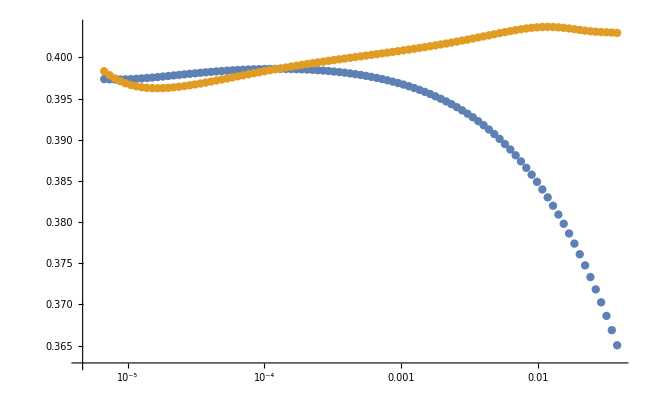

```mathematica
Show[ListPlot[{b1mub0,fitbeta},ScalingFunctions->{"Log"},PlotRange->{All,All}]]
```

```mathematica
Export["./NLObeta.dat",fitbeta]
```

./NLObeta.dat

```mathematica
fitbeta=Transpose[{-t[[2;;Length[t]-2]],Flatten[Table[NonlinearModelFit[datamub0[[i-1;;i+1]],fitfun2,{A,β,cm,θt1},x][[1]][[2]][[2]][[2]],{i,2,Length[t]-2}]]}];
```

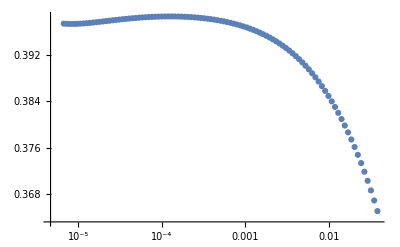

```mathematica
Show[ListPlot[fitbeta,ScalingFunctions->{"Log"},PlotRange->{All,All}]]
```

## Fit mub

```mathematica
(*A=Exp[1.532];*)
δ=4.79;
delta=4.79;
beta=0.397;
nu=0.759;
omega=0.6745;
θt=nu*omega;
fitfun=A x^β(1+cm x^θt1);
fitfun2=A+β x(*+Log[(1+cm Exp[x]^θt)]*);
fitfun3=A1+beta x+Log[(1+cm Exp[x]^θt)];
fitfun4=A+β x+Log[(1+cm Exp[x]^θt)];
```

```mathematica
fitbetamub500=Transpose[{-t[[2;;Length[t]-2]],Flatten[Table[NonlinearModelFit[datamub500[[i-1;;i+1]],fitfun4,{A,β,cm},x][[1]][[2]][[2]][[2]],{i,2,Length[t]-2}]]}];
```

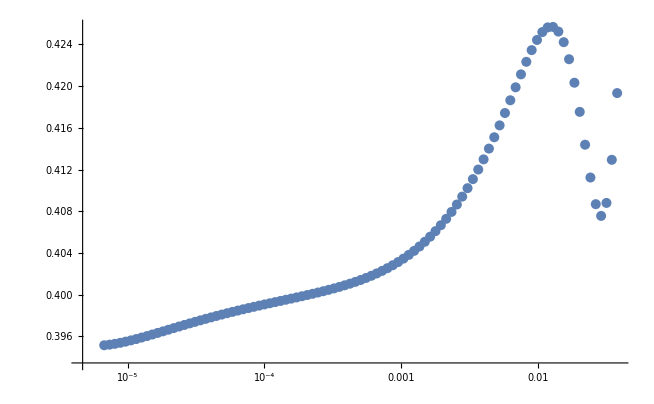

```mathematica
Show[ListPlot[{fitbetamub500},ScalingFunctions->{"Log"},PlotRange->{All,All}]]
```

```mathematica
Export["./NLObetamub500.dat",fitbetamub500]
```

./NLObetamub500.dat